# Grafico andamento Covid con dati rilevanti

## Intro:

### Crediti:

Dopo un tentativo di utilizzare i dati direttamente trasmessi dal ministero andato a vuoto (la formattazione dei dati del ministero della salute chiaramente non è pensata per una manipolazione comoda da parte di esterni) abbiamo deciso di utilizzare la repository italiana sull'andamento del Covid19 .

### Spiegazione:

Un ottimo esempio di crescita logistica è dato dalla diffusione di un virus, ed essendo verso la fine di una pandemia ci sembrava doveroso menzionarlo
perché l’andamento dei contagi segue una logistica?
Supponiamo di avere un numero di contagiati N_d al giorno d 
il numero di nuovi contagi ΔN_d dipende unicamente dal numero di persone contagiate, in quanto non ci sono altri fattori che contribuiscono al contagio
ergo ΔN_d = k N_d dove k possiamo pensarla come il coefficiente che tiene conto del numero di infetti che un non infetto incontra (in media) che possiamo chiamare “E” e la probabilità
 che quell’incontro risulti in un contagio, che possiamo chiamare “p” 
 
														 ΔN_d = E p N_d
														 
 Possiamo trasformare tale equazione in un’equazione differenziale
 N’=E p N la cui soluzione è banalmente un’esponenziale supponendo p ed E come costanti
 è Irrealistico però pensare che l’andamento sia un vero e proprio esponenziale, in quanto secondo questo ragionamento andando avanti col tempo il numero di contagi salirebbe all’infinito; non ha senso.
effettivamente non abbiamo tenuto conto di un fattore importante: non puoi ammalarti se sei già infetto.
ergo i nuovi contagi saranno sempre meno man mano che N_d raggiunge il numero totale di contagiabili (che chiameremo S)
Un’equazione più adeguata quindi sarà

														ΔN_d = k(1-N_d/S)N_d
														
 ergo													 N_(d+1) = N_d+ k (1-N_d/S)N_d
N_(d+1)= (N_d(1+k S -N_d))/S
N_(d+1)= 1/S N_d((k S +1)-N_d)
 che è chiaramente una mappa logistica.

## Codice:

```mathematica
ClearAll["Global`*"]
```

importiamo dalla repository sopra citata l’intera tabella aggiornata dei dati, eliminando tutte le liste con un singolo elemento (non interessanti poiché non contenenti dati)

```mathematica
tabellafull=Cases[Import["https://raw.githubusercontent.com/pcm-dpc/COVID-19/master/legacy/dati-andamento-nazionale/dpc-covid19-ita-andamento-nazionale.csv","CSV"] ,{_,__}];
```

breve tabella di quale numero corrisponde a quale dato:

```mathematica
Partition[Riffle[Range[Length[tabellafull⟦1⟧]],tabellafull⟦1⟧],2]
```

{{1,data},{2,stato},{3,ricoverati_con_sintomi},{4,terapia_intensiva},{5,totale_ospedalizzati},{6,isolamento_domiciliare},{7,totale_positivi},{8,variazione_totale_positivi},{9,nuovi_positivi},{10,dimessi_guariti},{11,deceduti},{12,totale_casi},{13,tamponi},{14,casi_testati},{15,note_it},{16,note_en}}

```mathematica
selectdata[n_]:= Drop[#⟦n⟧&/@tabellafull,1]
```

```mathematica
positivi =selectdata[12];
tamponi = selectdata[13];
Δpositivi=selectdata[9];
Δtamponi= Differences[Join[{0},tamponi]];
Δperc=(Δpositivi/Δtamponi)100. ;
```

il join in Δtamponi serve per aggiungere un elemento in cima alla lista così che la lista dei tamponi giornalieri avesse la stessa lunghezza di quella delle crescite

```mathematica
smoothTot = MovingMap[Mean,positivi,5];
smoothΔperc = MovingMap[Mean,Δperc,5];
```

e utilizzo una movingmap per tracciare la media coi 5 valori precedenti (così da rendere la curva un po’ più liscia)

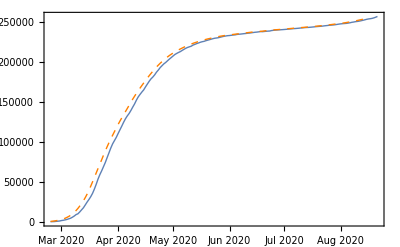

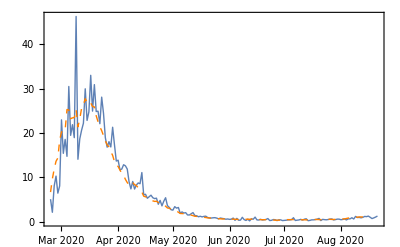

```mathematica
totPlot = DateListPlot[positivi,{2020,2,24},PlotStyle->{Thick}];
smoothTotPlot=DateListPlot[smoothTot,{2020,2,24},PlotStyle->{Orange,Dashed,Thick}];
Show[totPlot,smoothTotPlot]
percplot = DateListPlot[Δperc,{2020,2,24},PlotStyle->{Thick}];
smoothpercplot=DateListPlot[smoothΔperc,{2020,2,24},PlotStyle->{Orange,Dashed,Thick}];
Show[percplot,smoothpercplot]
```

il secondo grafico è la variazione, lo si può confrontare con la derivata del primo

```mathematica
modello = Normal[NonlinearModelFit[positivi,k/(1+q ⅇ^(-r x)),{k,q,r},x]]
Dmodello = D[modello, x]
```

241254./(1+30.9313 ⅇ^(-0.0808056 x))

(602994. ⅇ^(-0.0808056 x))/((1+30.9313 ⅇ^(-0.0808056 x))^2)

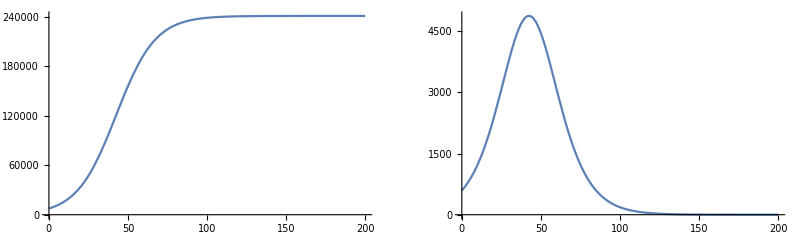

```mathematica
GraphicsRow[{Plot[modello,{x,0,200}],Plot[Dmodello,{x,0,200}]}]
```

la somiglianza è alquanto stretta